```mathematica
Clear["Global`*"]
```

```mathematica
(*units*)
```

```mathematica
e = 4.8032047*10^-10*cm^(3/2)*g^(1/2)/s;
c = 2.9979246 * 10^10*cm/s;
kB = 1.380649 * 10^(-16)* g*cm^2/(k*s^2);
m = 9.1094*10^(-28)*g;
tempv = 10 ^10 * k;
nv =  10^5 * (cm^-3);
Bv = 10 *cm^(-1/2)*g^(1/2)/s;
γ = thetaE;
θBv = 30*(Pi/180);
```

```mathematica
thetaE= kB*tempv/(m*c^2);
νB=e*Bv/(2*Pi*m*c);
νc = 3/2*νB*Sin[θBv]*γ^2;
```

```mathematica
Ii[x_]=2.5651(1+1.92x^(-1/3)+0.9977x^(-2/3))*Exp[-1.899x^(1/3)];
j[ν_]=nv*e^2*ν / (2*Sqrt[3]*c*thetaE^2)*Ii[(ν/νc)];
jx[x_]=nv*e^2*(x*νc) / (2*Sqrt[3]*c*thetaE^2)*Ii[x];
```

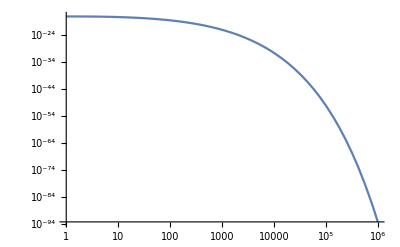

```mathematica
LogLogPlot[jx[x] /.{g->1, cm->1, s->1}, {x, 1,10^6}] 
LogLogPlot[j[x] /.{g->1, cm->1, s->1}, {x, 10^3,10^11}, PlotRange->{10^-20, 10^-17}];
```

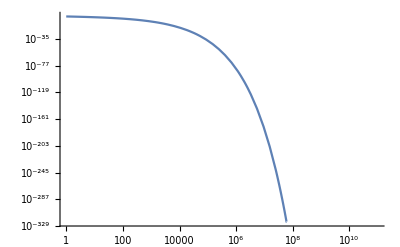

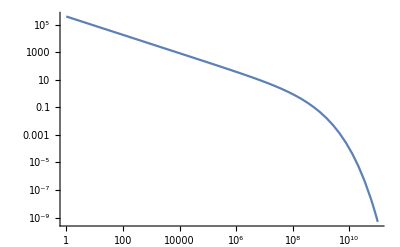

```mathematica
LogLogPlot[Ii[x], {x, 1,10^11}] 
LogLogPlot[Ii[x/νc]/.{g->1, cm->1, s->1}, {x, 1,10^11}]
```